Reproduce Ogasawara et al. [2017] plots, make sure they real

### The function, equation (1)

```mathematica
OgasaFunc[en_,phi0_,T_,kappa_,n_,mass_]:=n (mass/(2 π kappa T (1-3/(2 kappa))))^(3/2)2/mass^2 Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

#### After Spence has had his way

n in cm^-3
T in keV
energy in keV
phi0 in keV

```mathematica
OgasaFunc[en_,phi0_,T_,kappa_,n_]:=n (1/(2 π kappa T (1-3/(2 kappa))))^(3/2)(200*3*^8)/(√511)Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

Energy “pre-shifted” by phi0

```mathematica
OgasaFuncShift[en_,T_,kappa_,n_]:=n (1/(2 π kappa T (1-3/(2 kappa))))^(3/2)(200*3*^8)/(√511)Gamma[kappa+1]/Gamma[kappa-1/2](1+en/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

## Ogasawara-related stuff

### Parameters for Arc1

```mathematica
phi0=83/10; (*kV*)
T=14/10; (*keV*)
n=6/10; (*cm^-3*)
kappa=21;
```

```mathematica
fluxdivE={1*^7,7*^6,1.2*^6,6*^5,1.5*^5,5*^4,1.9*^4,1.2*^3,8*^1,9,4};
EminusPhi={2,4,6,7.5,9,11,13,18,21,31,39};
```

```mathematica
ogasaDat=Partition[Riffle[EminusPhi,fluxdivE],2]
```

{{2,10000000},{4,7000000},{6,1.2×10^6},{7.5,600000},{9,150000.},{11,50000},{13,19000.},{18,1200.},{21,80},{31,9},{39,4}}

```mathematica
ogasaModelDat=OgasaFuncShift[en,T,kappa,n];
```

```mathematica
constraints={1/100<ogN<2,1/10<ogT<10,3<ogKappa<35};
ogFitFunc = OgasaFuncShift[en,ogT,ogKappa,ogN];
```

```mathematica
ogStartT=14/10;ogStartKappa=3;ogStartN=6/10;
```

```mathematica
ogFit1=FindFit[ogasaDat,{ogFitFunc,constraints},{{ogT,ogStartT},{ogKappa,ogStartKappa},{ogN,ogStartN}},en]
```

{ogT→2.7288,ogKappa→35.,ogN→0.582718}

```mathematica
(*ogFit1={ogT->1.419,ogKappa->35.,ogN->0.58271}*)
```

{ogT→1.419,ogKappa→35.,ogN→0.58271}

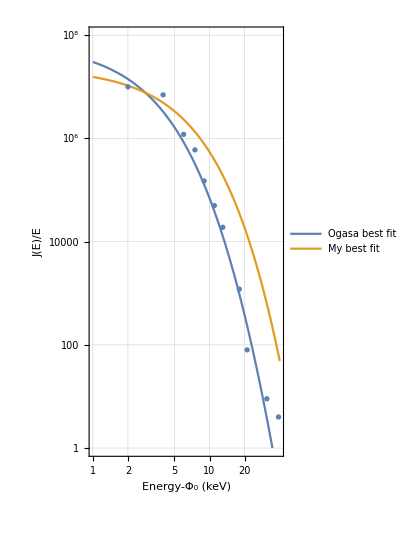

```mathematica
Show[LogLogPlot[{ogasaModelDat,ogFitFunc/.ogFit1},{en,1,40},PlotLegends->{"Ogasa best fit","My best fit"},PlotRange->{{1,40},{1,1*^8}},Frame->True,FrameLabel->{"Energy-Φ_0 (keV)","J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->18/10,ImageSize->300],ListLogLogPlot[ogasaDat]]
```

## FAST-related stuff

```mathematica
Needs["ErrorBarPlots`"]
```

#### Now a function for FAST

n in cm^-3, T in eV, Φ_0 in eV, en in eV

```mathematica
OgasaFuncFAST[en_,phi0_,T_,kappa_,n_]:=n (1/(π kappa T (1-3/(2 kappa))))^(3/2)(3*^8)/(√(1022/10))Gamma[kappa+1]/Gamma[kappa-1/2](1+(en-phi0)/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

```mathematica
MaxwellFuncFAST[en_,phi0_,T_,n_]:=n (1/(π T))^(3/2)(3*^8)/(√(1022/10))Exp[-(en-phi0)/T]
```

```mathematica
OgasaFuncFASTShift[en_,T_,kappa_,n_]:=n (1/(π kappa T (1-3/(2 kappa))))^(3/2)(3*^8)/(√(1022/10))Gamma[kappa+1]/Gamma[kappa-1/2](1+en/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
```

```mathematica
OgasaFuncFASTShiftkeV[en_,T_,kappa_,n_]:=n (1/(π kappa T (1-3/(2 kappa))))^(3/2)(3*^7)/(√1022)Gamma[kappa+1]/Gamma[kappa-1/2](1+en/(kappa T (1-3/(2 kappa))))^(-(kappa+1))
MaxwellFuncFASTShiftkeV[en_,T_,n_]:=n (1/(π  T))^(3/2)(3*^7)/(√1022)Exp[-en/T]
```

### Other helper functions

```mathematica
makeErrorDataOld[energies_,fluxDivE_,errorsDivE_]:=Module[{zeList},
eAndFlux=Partition[Riffle[energies,fluxDivE],2];
errorB=Map[ErrorBar,errorsDivE];
zeList=Partition[Riffle[eAndFlux,errorB],2]
];
```

```mathematica
makeErrorData[energies_,fluxDivE_,errorsDivE_]:=Module[{zeList},
eAndFlux=Partition[Riffle[energies,fluxDivE],2];
zeList=Partition[Flatten[Riffle[eAndFlux,errorsDivE]],3]
];
```

```mathematica
makeLogErrorData[energies_,fluxDivE_,errorsDivE_]:=Module[{zeList,eAndFlux,tmpList},
eAndFlux=Partition[Riffle[energies,fluxDivE],2];
tmpList=Partition[Flatten@Riffle[eAndFlux,errorsDivE],3];
zeList={{Log10[#[[1]]],Log10[#[[2]]]},ErrorBar[Log10[1+0.5#]&/@{-#[[3]]/#[[2]],#[[3]]/#[[2]]}]}&/@tmpList
];
```

```mathematica
LogErrorListPlot[errorData_]:=Module[{logErrorPlot,plotrange,xticks,yticks,xt,yt,logData},
plotrange={Floor@Log10@Min[#],Ceiling@Log10@Max[#]}&@errorData[[All,#]]&/@{1,2};
xticks={#,Superscript[10,#]}&/@Range[#1,#2,1]&@@plotrange[[1]];
yticks={#,Superscript[10,#]}&/@Range[#1,#2,1]&@@plotrange[[2]];
{xt,yt}=#~Join~({#,""}&/@Flatten[(#[[1]]+Log10[{2,3,4,5,6,7,8,9}])&/@#])&/@{xticks,yticks};
logData={{Log10[#[[1]]],Log10[#[[2]]]},ErrorBar[Log10[1+0.5#]&/@{-#[[3]]/#[[2]],#[[3]]/#[[2]]}]}&/@errorData;
logErrorPlot=ErrorListPlot[logData,Joined->True,PlotRange->plotrange,FrameTicks->{{yt,None},{xt,None}},GridLines->{xt[[All,1]],yt[[All,1]]},Frame->True,Axes->False,FrameLabel->{"Energy (eV)","J(E)/E"},FrameStyle->(FontSize->18),AspectRatio->14/10,ImageSize->500]
];
```

### Data from my arc

```mathematica
energies={815.4,940.8,1129.,1380.,1631.,1882.,2258.,2760.,3261.,3763.,4516.,5519.,6523.,7526.,9032.,1.104*^4,1.305*^4,1.505*^4,2.208*^4,3.011*^4};
flux={7.113*^5,7.245*^5,4.415*^5,1.694*^5,6.177*^4,2.504*^4,1.032*^4,3854.,2237.,1246.,428.6,417.9,193.8,108.6,32.97,20.04,5.744,4.978,6.748,2.489};
errors={2.670*^4,2.509*^4,1.788*^4,1.001*^4,5558.,3292.,1911.,1058.,733.7,503.6,242.3,205.9,126.7,64.71,22.51,16.13,5.744,4.978,4.772,2.489};
```

```mathematica
(*energies={815.4,940.8,1129.,1380.,1631.,1882.,2258.,2760.,3261.,3763.,4516.,5519.,6523.,7526.,9032.,1.104*^4,1.305*^4,1.505*^4,1.806*^4,2.208*^4,2.609*^4,3.011*^4};
flux={7.113*^5,7.245*^5,4.415*^5,1.694*^5,6.177*^4,2.504*^4,1.032*^4,3854.,2237.,1246.,428.6,417.9,193.8,108.6,32.97,20.04,5.744,4.978,0.000,6.748,0.000,2.489};
errors={2.670*^4,2.509*^4,1.788*^4,1.001*^4,5558.,3292.,1911.,1058.,733.7,503.6,242.3,205.9,126.7,64.71,22.51,16.13,5.744,4.978,0.000,4.772,0.000,2.489};*)
```

```mathematica
spenceDat=makeErrorDataOld[energies,flux/energies,errors/energies];
```

```mathematica
spenceLogDat=makeErrorData[Log10[energies],Log10[flux/energies],Log10[errors/energies]]
```

{{2.91137,2.94068,1.51514},{2.9735,2.88654,1.426},{3.05269,2.59224,1.19967},{3.13988,2.08903,0.860555},{3.21245,1.57832,0.532465},{3.27462,1.12401,0.24284},{3.35372,0.659956,-0.0724633},{3.44091,0.145003,-0.416423},{3.51335,-0.163685,-0.647832},{3.57553,-0.480016,-0.873448},{3.65475,-1.0227,-1.2704},{3.74186,-1.12079,-1.4282},{3.81445,-1.52709,-1.71167},{3.87656,-1.84073,-2.06559},{3.95578,-2.43766,-2.60341},{4.04297,-2.74107,-2.83533},{4.11561,-3.3564,-3.3564},{4.17754,-3.48048,-3.48048},{4.344,-3.51482,-3.6653},{4.47871,-4.08269,-4.08269}}

```mathematica
showError=1;
```

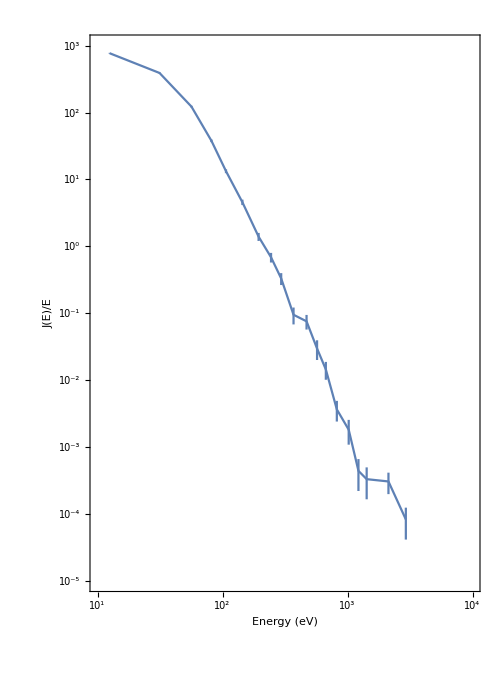

```mathematica
LogErrorListPlot[makeErrorData[(energies[[2;;]]-energies[[1]])/10,flux[[2;;]]/energies[[2;;]],errors[[2;;]]/energies[[2;;]]]]
```

```mathematica
phi0=940;
T=353;
kappa=163/100;
dens=0.28;
```

```mathematica
modelData=Partition[Riffle[energies,OgasaFuncFAST[energies,phi0,T,kappa,dens]],2]
```

{{815.4,-717.738-1658.6 ⅈ},{940.8,7136.97},{1129.,101.906},{1380.,15.0653},{1631.,5.03853},{1882.,2.33071},{2258.,0.997936},{2760.,0.437665},{3261.,0.234145},{3763.,0.141184},{4516.,0.0764844},{5519.,0.040212},{6523.,0.0239862},{7526.,0.0155835},{9032.,0.00909759},{11040.,0.00509365},{13050.,0.00316653},{15050.,0.00212133},{22080.,0.000734632},{30110.,0.000315496}}

```mathematica
logModelData={{Log10[#[[1]]],Log10[#[[2]]]}}&/@modelData;
```

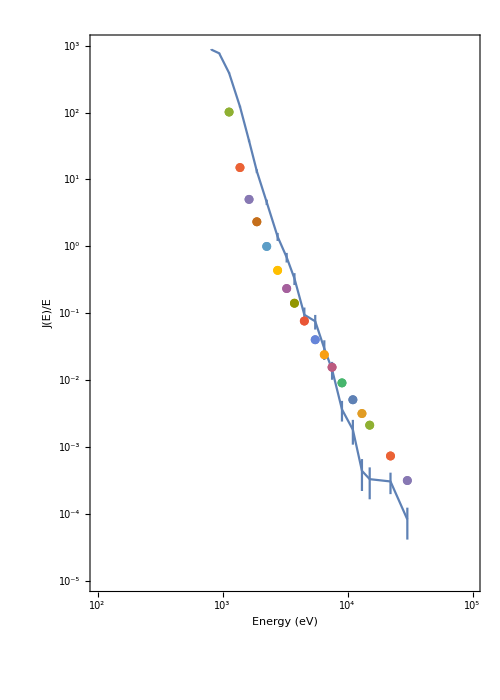

```mathematica
Show[LogErrorListPlot@makeErrorData[energies,flux/energies,errors/energies],ListPlot[logModelData,InterpolationOrder->3]]
```

### Fits

```mathematica
constraints={0.001<fitN<4,10<fitT<5000,1.51<fitKappa<35};
```

```mathematica
FASTModel = OgasaFuncFASTShift[en,fitT,fitKappa,fitN];
```

```mathematica
eAndFlux=Partition[Riffle[energies[[3;;]]-energies[[2]],flux[[3;;]]/energies[[3;;]]],2]
```

{{188.2,391.054},{439.2,122.754},{690.2,37.8725},{941.2,13.305},{1317.2,4.57042},{1819.2,1.39638},{2320.2,0.685986},{2822.2,0.331119},{3575.2,0.094907},{4578.2,0.0757202},{5582.2,0.0297103},{6585.2,0.01443},{8091.2,0.00365035},{10099.2,0.00181522},{12109.2,0.000440153},{14109.2,0.000330764},{21139.2,0.000305616},{29169.2,0.0000826636}}

Kappa fit

```mathematica
fitter=FindFit[eAndFlux,{FASTModel,constraints},{fitT,fitKappa,fitN},en]
```

{fitT→222.135,fitKappa→34.9986,fitN→0.565268}

```mathematica
fitter={fitT->222.1346149321158,fitKappa->3.9,fitN->0.6};
```

```mathematica
fitter=FindFit[eAndFlux,{FASTModel,constraints},{fitT,fitKappa,fitN},en]
```

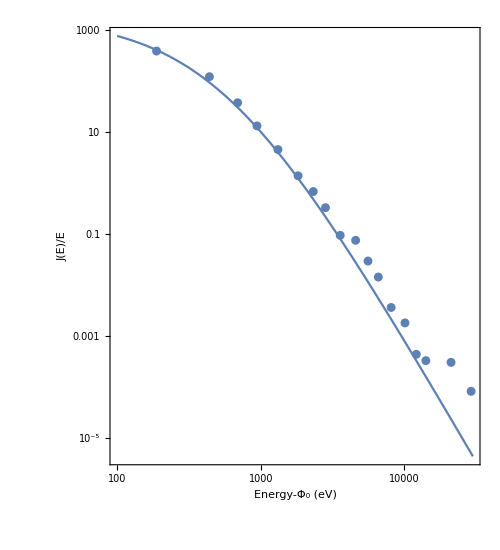

```mathematica
Show[LogLogPlot[FASTModel/.fitter,{en,100,30000},Frame->True,FrameLabel->{"Energy-Φ_0 (eV)","J(E)/E"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->11/10,ImageSize->500],ListLogLogPlot[eAndFlux]]
```

#### Try keV energies

```mathematica
startInd=3;
```

```mathematica
constraints={0.001<fitN<4,0.01<fitT<5,1.51<fitKappa<35};
constraintsMaxwell={0.001<GfitN<4,0.01<GfitT<5};
```

```mathematica
FASTModelkeV = OgasaFuncFASTShiftkeV[en,fitT,fitKappa,fitN];
```

```mathematica
FASTModelMaxwellkeV = MaxwellFuncFASTShiftkeV[en,GfitT,GfitN];
```

```mathematica
eAndFluxkeV=Partition[Riffle[(energies[[startInd;;]]-energies[[startInd-1]])/1000,flux[[startInd;;]]/energies[[startInd;;]]*1000],2];
```

```mathematica
fitter=FindFit[eAndFluxkeV,{FASTModelkeV,constraints},{fitT,fitKappa,fitN},en]
```

{fitT→0.222134,fitKappa→35.,fitN→0.565268}

```mathematica
fitter={fitT->0.250,fitKappa->3.9,fitN->0.6};
```

```mathematica
Gfitter=FindFit[eAndFluxkeV,{FASTModelMaxwellkeV,constraintsMaxwell},{GfitT,GfitN},en]
```

{GfitT→0.216801,GfitN→0.557958}

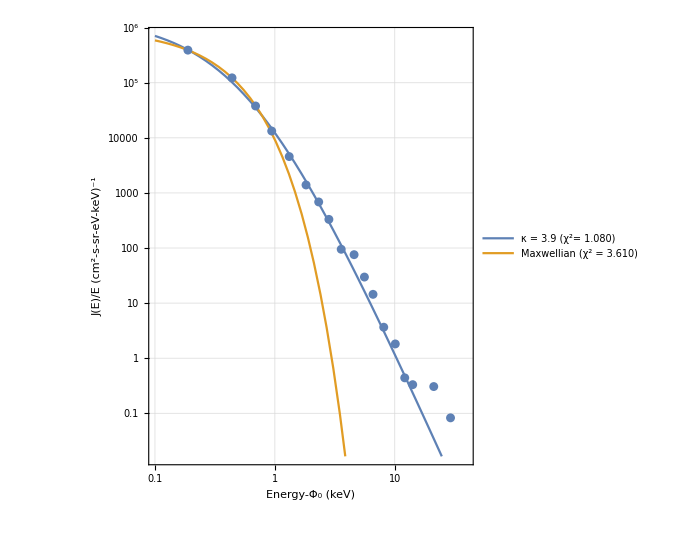

```mathematica
Show[LogLogPlot[{FASTModelkeV/.fitter,FASTModelMaxwell/.Gfitter},{en,0.1,40},PlotRange->{Automatic,{Min[eAndFluxkeV[[All,2]]]/5,Automatic}},PlotLegends->((Style[#,18])&/@{StringForm["κ = `1`       (χ^2= `2`)",fitKappa,NumberForm[chiSqCalc[fitter],{3,3}]]/.fitter,StringForm["Maxwellian (χ^2 = `1`)",NumberForm[GchiSqCalc[Gfitter],{3,3}]]}),Frame->True,FrameLabel->{"Energy-Φ_0 (keV)","J(E)/E (cm^2-s-sr-eV-keV)^-1"},FrameTicks->Automatic,GridLines->Full,FrameStyle->(FontSize->18),AspectRatio->11/10,ImageSize->500],ListLogLogPlot[eAndFluxkeV]]
```

```mathematica
F=Length@energies[[3;;]]-4;
GF=Length@energies[[3;;]]-3;
```

```mathematica
rules=(Append[fitter,en->#/1000]&/@(energies[[startInd;;]]-energies[[startInd-1]]));
```

```mathematica
modelData=(FASTModelkeV/.#)&/@rules
```

{392950.,86990.5,29174.6,12379.9,4484.91,1573.64,687.741,346.086,147.988,59.6786,28.4646,15.253,6.95697,2.96551,1.46804,0.809684,0.166113,0.0466753}

```mathematica
chiSq=1/F * Total[(eAndFluxkeV[[All,2]]-modelData)^2/(errors[[startInd;;]]/energies[[startInd;;]]*1000)^2]
```

3.07624

### χ_red^2 calculation

```mathematica
chiSqCalc[fitter_]:=Module[{chiSq,rules,modelData},
rules=(Append[fitter,en->#/1000]&/@(energies[[startInd;;]]-energies[[startInd-1]]));
modelData=(FASTModelkeV/.#)&/@rules;
chiSq=1/F * Total[(eAndFluxkeV[[All,2]]-modelData)^2/(errors[[startInd;;]]/energies[[startInd;;]]*1000)^2]
];
GchiSqCalc[Gfitter_]:=Module[{GchiSq,rules,modelData},
rules=(Append[Gfitter,en->#/1000]&/@(energies[[startInd;;]]-energies[[startInd-1]]));
modelData=(FASTModelMaxwellkeV/.#)&/@rules;
GchiSq=1/GF * Total[(eAndFluxkeV[[All,2]]-modelData)^2/(errors[[startInd;;]]/energies[[startInd;;]]*1000)^2]
];
```

```mathematica
fitterList=({fitT->0.250,fitKappa->#,fitN->0.6})&/@{1.6,1.7,1.8,2.0,2.3,2.5,3.0,3.9,4.2,5.0,10,30}
```

{{fitT→0.25,fitKappa→1.6,fitN→0.6},{fitT→0.25,fitKappa→1.7,fitN→0.6},{fitT→0.25,fitKappa→1.8,fitN→0.6},{fitT→0.25,fitKappa→2.,fitN→0.6},{fitT→0.25,fitKappa→2.3,fitN→0.6},{fitT→0.25,fitKappa→2.5,fitN→0.6},{fitT→0.25,fitKappa→3.,fitN→0.6},{fitT→0.25,fitKappa→3.9,fitN→0.6},{fitT→0.25,fitKappa→4.2,fitN→0.6},{fitT→0.25,fitKappa→5.,fitN→0.6},{fitT→0.25,fitKappa→10,fitN→0.6},{fitT→0.25,fitKappa→30,fitN→0.6}}

```mathematica
(chiSqCalc[#])&/@fitterList
```

{53.5158,49.8582,45.8074,33.2091,16.7284,10.1047,3.02773,1.07879,1.07455,1.29398,2.63764,4.09111}

## Derivatives

### Derivatives for IDL function KAPPA_FLUX__LINEAR_SHIFT_IN_ENERGY__JE_OVER_E

```mathematica
kapDerivs=FullSimplify@D[OgasaFuncFAST[en,modphi0,modT,modkappa,modn],#]&/@{modphi0,modT,modkappa,modn}/.{modphi0->ΔΦ,modT->Tm,modkappa->κ,modn->nm}
```

{(1200000000 √(10/511) nm √(1/(Tm (-3+2 κ))) (1+(2 (en-ΔΦ))/(Tm (-3+2 κ)))^-κ Gamma[2+κ])/(π^(3/2) (2 en-2 ΔΦ+Tm (-3+2 κ))^2 Gamma[-1/2+κ]),-(300000000 √(10/511) nm √(1/(Tm (-3+2 κ))) (-9 Tm-2 ΔΦ+en (2-4 κ)+6 Tm κ+4 ΔΦ κ) (1+(2 (en-ΔΦ))/(Tm (-3+2 κ)))^-κ Gamma[1+κ])/(π^(3/2) Tm (2 en-2 ΔΦ+Tm (-3+2 κ))^2 Gamma[-1/2+κ]),1/(π^(3/2) Tm (3-2 κ)^2 Gamma[-1/2+κ])600000000 √(10/511) nm √(1/(Tm (-3+2 κ))) (1+(2 (en-ΔΦ))/(Tm (-3+2 κ)))^(-1-κ) Gamma[1+κ] (-3+(4 (en-ΔΦ) (1+κ))/(2 en-2 ΔΦ+Tm (-3+2 κ))+(3-2 κ) Log[1+(2 (en-ΔΦ))/(Tm (-3+2 κ))]+(3-2 κ) PolyGamma[0,-1/2+κ]+(-3+2 κ) PolyGamma[0,1+κ]),(600000000 √(10/511) κ (-1/(3 π Tm-2 π Tm κ))^(3/2) (1+(2 (en-ΔΦ))/(Tm (-3+2 κ)))^(-1-κ) Gamma[κ])/Gamma[-1/2+κ]}

```mathematica
D[Gamma[k+1]/((k-3/2)^(3/2)Gamma[k-1/2]),k]//FullSimplify
```

(2 √2 k Gamma[k] (-3+(3-2 k) HarmonicNumber[-3/2+k]+(-3+2 k) HarmonicNumber[k]))/((-3+2 k)^(5/2) Gamma[-1/2+k])

```mathematica
D[(1+a/(k-3/2))^(-(k+1)),k]
```

(1+a/(-3/2+k))^(-1-k) (-(a (-1-k))/((1+a/(-3/2+k)) (-3/2+k)^2)-Log[1+a/(-3/2+k)])

Maswell

```mathematica
D[1/Tm^(3/2)Exp[-a/Tm],Tm]//FullSimplify
```

(ⅇ^(-a/Tm) (2 a-3 Tm))/(2 Tm^(7/2))

```mathematica
( a-3/2 Tm)/Tm
```

### Test derivatives

```mathematica
energies={815.4,940.8,1129.,1380.,1631.,1882.,2258.,2760.,3261.,3763.,4516.,5519.,6523.,7526.,9032.,1.104*^4,1.305*^4,1.505*^4,2.208*^4,3.011*^4};
```

```mathematica
repl={ΔΦ-> energies[[2]],Tm-> 222,κ-> 39/10,nm-> 6/10};
```

```mathematica
kapDerivs/.repl
```

{(300000000 √(2/18907) Gamma[59/10])/((1+(5 (-940.8+en))/2664)^(39/10) (-816.+2 en)^2 π^(3/2) Gamma[17/5]),-(12500000 √(2/18907) (15991.7-(68 en)/5) Gamma[49/10])/(37 (1+(5 (-940.8+en))/2664)^(39/10) (-816.+2 en)^2 π^(3/2) Gamma[17/5]),(9765625 √(2/18907) Gamma[49/10] (-3+(98 (-940.8+en))/(5 (-816.+2 en))-24/5 Log[1+(5 (-940.8+en))/2664]-24/5 PolyGamma[0,17/5]+24/5 PolyGamma[0,49/10]))/(333 (1+(5 (-940.8+en))/2664)^(49/10) π^(3/2) Gamma[17/5]),(101562500 √(2/18907) Gamma[39/10])/(111 (1+(5 (-940.8+en))/2664)^(49/10) π^(3/2) Gamma[17/5])}

```mathematica
Table[{i,energies[[i]],flux[[i]]}~Join~(kapDerivs/.repl)/.en->energies[[i]],{i,1,Length@energies}]//TableForm
```

1 | 815.4 | 711300. | 80.7432 | -90.9686 | -3832.69 | 11188.7
2 | 940.8 | 724500. | 16.5768 | -12.1789 | -380.016 | 3004.13
3 | 1129. | 441500. | 2.78235 | -0.407505 | 8.02665 | 682.339
4 | 1380. | 169400. | 0.477528 | 0.304691 | 10.4664 | 157.877
5 | 1631. | 61770. | 0.123144 | 0.175182 | 3.39534 | 51.2263
6 | 1882. | 25040. | 0.040935 | 0.0903476 | 0.926694 | 20.5232
7 | 2258. | 10320. | 0.0107131 | 0.0362352 | -0.00792035 | 6.74126
8 | 2760. | 3854. | 0.00259866 | 0.0128669 | -0.145365 | 2.07893
9 | 3261. | 2237. | 0.000831667 | 0.0054202 | -0.110612 | 0.807057
10 | 3763. | 1246. | 0.000319628 | 0.00258461 | -0.072976 | 0.364745
11 | 4516. | 428.6 | 0.0000967856 | 0.00101043 | -0.0386648 | 0.135236
12 | 5519. | 417.9 | 0.0000266714 | 0.000362059 | -0.0178883 | 0.0463665
13 | 6523. | 193.8 | 9.25744×10^-6 | 0.000154719 | -0.00909685 | 0.0192549
14 | 7526. | 108.6 | 3.77849×10^-6 | 0.0000749948 | -0.00501802 | 0.00914805
15 | 9032. | 32.97 | 1.21772×10^-6 | 0.0000299011 | -0.00231349 | 0.00357199
16 | 11040. | 20.04 | 3.54162×10^-7 | 0.0000109192 | -0.000972066 | 0.00128077
17 | 13050. | 5.744 | 1.27502×10^-7 | 4.73205×10^-6 | -0.000467723 | 0.000548259
18 | 15050. | 4.978 | 5.36028×10^-8 | 2.32447×10^-6 | -0.000249385 | 0.000266957
19 | 22080. | 6.748 | 5.30183×10^-9 | 3.46408×10^-7 | -0.0000451395 | 0.0000390821
20 | 30110. | 2.489 | 8.25647×10^-10 | 7.46681×10^-8 | -0.0000111437 | 8.34128×10^-6